```mathematica
root = "/home/boxx/bees";
datadir = FileNameJoin[{root, "images4nets"}];
bifariousdir=FileNameJoin[{datadir, "B_bifarious_just_cropped"}];
melanopygusdir = FileNameJoin[{datadir, "B_melanopygus_just_cropped"}];
bifariousdir1=FileNameJoin[{datadir, "B_bifarious_zoom"}];
melanopygusdir1 = FileNameJoin[{datadir, "B_melanopygus_zoom"}];
bifariousdir0=FileNameJoin[{datadir, "B_bifarious_rotate"}];
melanopygusdir0 = FileNameJoin[{datadir, "B_melanopygus_rotate"}];
bifarfiles=FileNames["*.jpg", bifariousdir];
melanofiles = FileNames["*.jpg", melanopygusdir];
bifarfiles1=FileNames["*.jpg", bifariousdir1];
melanofiles1 = FileNames["*.jpg", melanopygusdir1];
bifarfiles0=FileNames["*.jpg", bifariousdir0];
melanofiles0 = FileNames["*.jpg", melanopygusdir0];
{Length@bifarfiles0, Length@melanofiles0}
```

{3106,2846}

```mathematica
Needs["CUDALink`"]
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx10g"];
```

```mathematica
bifardat=ParallelMap[Import[#]&,bifarfiles];
melanodat=ParallelMap[Import[#]&,melanofiles];
bifardat0=ParallelMap[Import[#]&,bifarfiles0];
melanodat0=ParallelMap[Import[#]&,melanofiles0];
bifardat1=ParallelMap[Import[#]&,bifarfiles1];
melanodat1=ParallelMap[Import[#]&,melanofiles1];
```

```mathematica
{Dimensions@bifardat, Dimensions@melanodat}
```

{{1553},{1423}}

```mathematica
RandomSample[bifardat, 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[melanodat,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dat=RandomSample@Join[Thread[bifardat->"bifar"],Thread[melanodat->"melano"], Thread[bifardat0->"bifar"],Thread[melanodat0->"melano"], Thread[bifardat1->"bifar"],Thread[melanodat1->"melano"]];
Dimensions@dat
```

{14880}

```mathematica
RandomSample[dat,30]
```

{-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano}

```mathematica
bifEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,bifardat0];
melEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,melanodat0];
```

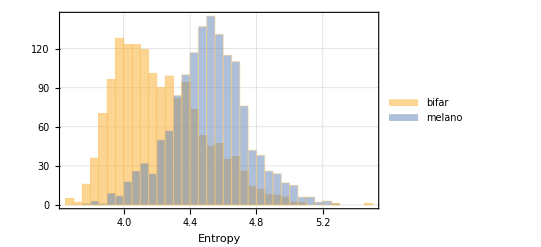

```mathematica
Histogram[{bifEntropy,melEntropy},40,ChartLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

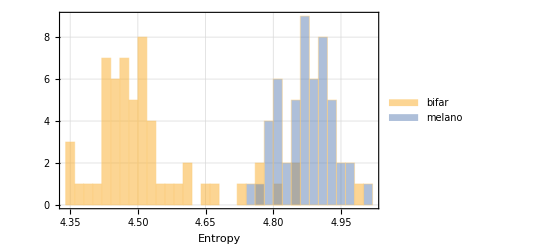

```mathematica
Histogram[{Map[Mean,Partition[bifEntropy,108]],Map[Mean,Partition[melEntropy,108]]},40,ChartLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

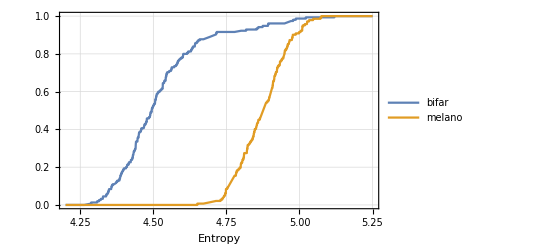

```mathematica
Plot[{CDF[EmpiricalDistribution[Map[Mean, Partition[bifEntropy,40]]],x], CDF[EmpiricalDistribution[Map[Mean, Partition[melEntropy, 40]]],x]},{x,4.2,5.25},PlotLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

```mathematica
rs=RandomSample[Range[Length[dat]]];
tix=rs[[1;;Round[Length[dat]*0.7]]];
vix=rs[[Round[Length[dat]*0.7]+1;;Round[Length[dat]*0.9]]];
ttix=rs[[Round[Length[dat]*0.9]+1;;]];
{Length@tix,Length@vix,Length@ttix}
```

{10416,2976,1488}

```mathematica
networkdir=FileNameJoin[{root,"networks"}];
net=NetChain[
{
ConvolutionLayer[40,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{3,3},{2,2}],
ConvolutionLayer[80,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DropoutLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"bifar","melano"}}],
"Input"->NetEncoder[{"Image",{220,298}}]
]
```

NetChain[<>]

```mathematica
net=NetTrain[net,dat[[tix]],ValidationSet->dat[[vix]],TargetDevice->"GPU","Method"->{"ADAM","L2Regularization"->5,"InitialLearningRate"->0.0001}, MaxTrainingRounds->10];
```

```mathematica
%61
```

NetChain[<>]

```mathematica
cm=ClassifierMeasurements[net,dat[[ttix]]];
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.925403

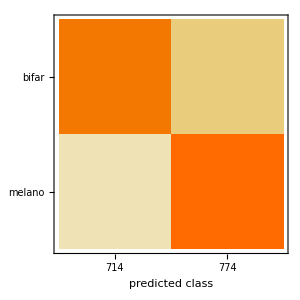

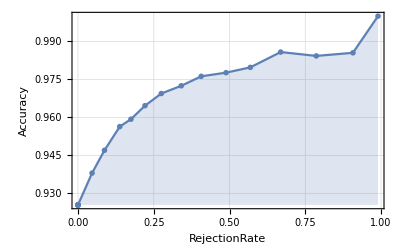

```mathematica
cm["ConfusionMatrixPlot"]
cm["AccuracyRejectionPlot"]
```

```mathematica
testDatBifar=Select[dat[[ttix]],Values@#=="bifar"&];
testDatMelano=Select[dat[[ttix]],Values@#=="melano"&];
```

```mathematica
pTestDatBifar=net[Keys@testDatBifar,{"Probability","bifar"}];
pTestDatMelano=net[Keys@testDatMelano,{"Probability","bifar"}];
```

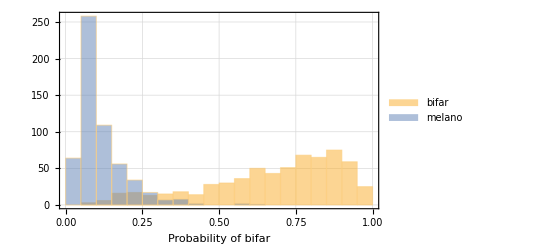

```mathematica
Histogram[{pTestDatBifar,pTestDatMelano},20,GridLines->Automatic,GridLinesStyle->Directive[Dotted,Gray],Frame->True,FrameLabel->{"Probability of bifar"},ChartLegends->{"bifar","melano"}]
```

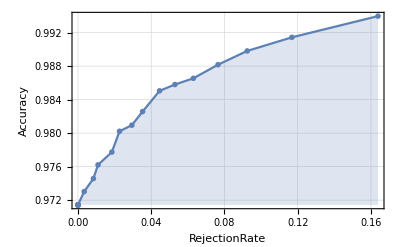

```mathematica
Show[
cm["AccuracyRejectionPlot"],
GridLines->Automatic,
GridLinesStyle->Directive[Dotted, Gray]
]
```